```mathematica
𝒞=2294983143867199389062902249401714330350557788401050858543666731289730975449453862557885685417959029567369443334864162957368534233575170403874130599990298613542760495071
```

2294983143867199389062902249401714330350557788401050858543666731289730975449453862557885685417959029567369443334864162957368534233575170403874130599990298613542760495071

```mathematica
PrimeQ[𝒞]
```

False

```mathematica
Timing[FactorInteger[𝒞]]
```

$Aborted

```mathematica
𝒬=√𝒞//N//Ceiling
```

1514920177391270709605807832941731980812936097930035636302558974900205847057455382528

```mathematica
Mod[𝒞, 𝒬-i]/.i-> -10^19//Log10//N
```

83.365

```mathematica
PrimeQ[31]
```

True

```mathematica
PrimeQ[73]
```

True

```mathematica
𝒞=73 31
```

2263

```mathematica
𝒬=√𝒞//N//Round
```

48

```mathematica
𝒮1=SortBy[Counts[Table[Mod[𝒞, 𝒬-i], {i,0,𝒬-2}]], #1]
```

<|0→1,1→7,2→3,3→4,4→1,6→1,7→6,8→2,9→3,13→5,16→1,19→4,21→1,22→1,23→4,27→1,31→1,37→1|>

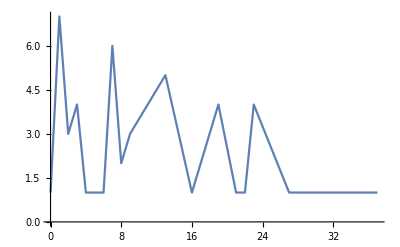

```mathematica
ListLinePlot[𝒮1]
```

```mathematica
𝒮2=SortBy[Counts[Table[Mod[𝒞, 𝒬+i], {i,0,𝒬-2}]], #1]
```

<|0→1,1→3,6→1,7→2,8→1,9→1,13→3,19→3,21→1,22→1,23→4,27→2,30→1,31→3,37→1,38→1,40→1,43→2,49→2,51→1,52→1,53→2,55→2,58→1,59→1,62→1,63→1,76→1,79→2|>

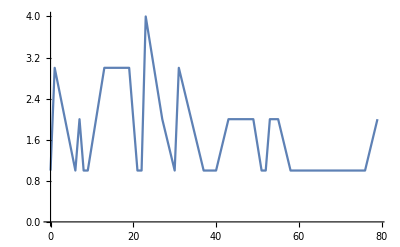

```mathematica
ListLinePlot[𝒮2]
```

```mathematica
FactorInteger[𝒞]
```

{{31,1},{73,1}}

```mathematica
FactorsZone[n_]:= Module[{
},
𝒫1=Prime[n];
𝒫2=Prime[2n];
Print[𝒫1,", ", 𝒫2];
𝒞=𝒫1 𝒫2;
𝒬=√𝒞;
Print[𝒬];
𝒮=SortBy[Join[Counts[Table[Mod[𝒞, 𝒬+i], {i,-𝒬+2,𝒬-2, 10}]],<|𝒞->0|>], #1];
Show[ListLinePlot[𝒮, {ImageSize->Medium}],Graphics[{Red,Thick, Line[{{𝒫1,0}, {𝒫1, 8}}]}],Graphics[{Purple,Thick,Line[{{𝒫2,0}, {𝒫2, 8}}]}], Graphics[{Green,Thick, Line[{{𝒬,0}, {𝒬, 8}}]}], Graphics[{Black,Thick, Line[{{𝒞,0}, {𝒞, 1}}]}]]
]
```

541, 1223

√661643

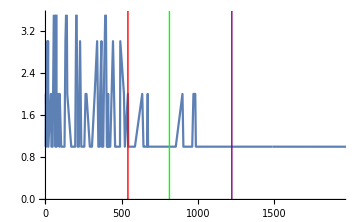

```mathematica
FactorsZone[100]
```